# WolframModel

Generate evolutions of Wolfram model systems

## DefinitionDefinitionDefine your function using the name you gave in the Title line above. You can add input cells and extra code to define additional input cases or prerequisites. All definitions, including dependencies, will be included in the generated resource function. This section should be evaluated before creating the Examples section below.

### loadPaclet

```mathematica
randomID[]:=IntegerString[RandomInteger[1*^18],36]
```

```mathematica
savePacletFile[pacletByteArray_]:=With[{directory=CreateDirectory@FileNameJoin@{$TemporaryDirectory,randomID[]}},
Export[FileNameJoin@{directory,"paclet.zip"},Normal@pacletByteArray,"Byte"]
];
```

```mathematica
unpackPaclet[pacletByteArray_]:=Module[{directory,pacletFile},
directory=FileNameJoin@Most@FileNameSplit@(pacletFile=savePacletFile@pacletByteArray);
ExtractArchive[pacletFile,directory];
directory
];
```

```mathematica
secretlyLoadPaclet[directory_,context_]:=(
PacletDirectoryLoad[directory];
Quiet[Get[context],General::shdw];
$ContextPath=DeleteCases[$ContextPath,context];
PacletDirectoryUnload[directory];
)
```

```mathematica
loadPaclet[context_,pacletByteArray_]:=Once@secretlyLoadPaclet[unpackPaclet@pacletByteArray,context]
```

### pacletContext

```mathematica
pacletContext[pacletByteArray_]:=With[{filename=savePacletFile@pacletByteArray},First@PacletObject[RenameFile[filename,FileNameJoin@Append["p.paclet"]@Most@FileNameSplit@filename]]@"Context"]
```

### Translation

Source Code: https://github.com/maxitg/SetReplace

```mathematica
$setReplace=ByteArray[…];
```

```mathematica
$setReplaceDesktopContext=pacletContext@$setReplace;
```

```mathematica
$setReplaceCloudContext="SetReplace`";
```

```mathematica
setReplaceContext[]:=If[$CloudEvaluation,$setReplaceCloudContext,$setReplaceDesktopContext]
```

input should be held.

```mathematica
wfrEvaluate[input_]:=Module[{result,symbolToWFRRules},
If[$CloudEvaluation,<<SetReplace`,loadPaclet[$setReplaceDesktopContext,$setReplace]];
result=ReleaseHold@input;
symbolToWFRRules=Union@Cases[result,s_Symbol?(Context@#===setReplaceContext[]&):>s->ResourceFunction@SymbolName@s,All,Heads->True];
(result/.symbolToWFRRules)/;With[{r=result},Hold[r]]=!=input
]
```

```mathematica
WolframModel/:RulePlot[WolframModel[args___],opts___]:=With[{result=wfrEvaluate[With[{headSymbol=Symbol[setReplaceContext[]<>"WolframModel"]},Hold[RulePlot[headSymbol[args],opts]]]]},
result/;Head[result]=!=wfrEvaluate
]
```

```mathematica
WolframModel[args___]:=With[{result=wfrEvaluate[With[{headSymbol=Symbol[setReplaceContext[]<>"WolframModel"]},Hold[headSymbol[args]]]]},
result/;Head[result]=!=wfrEvaluate
]
```

## Documentation

### UsageUsageDocument input usage cases by first typing an input structure, then pressing to add a brief explanation of the function’s behavior for that structure. Pressing repeatedly will create new cases as needed. Every input usage case defined above should be demonstrated explicitly here. See existing documentation pages for examples.

WolframModel[rules,init,t]

generates an object representing the evolution of the Wolfram model with the specified rules from the initial condition init for t generations.

WolframModel[rules,init,t,prop]

gives the property prop of the evolution.

WolframModel[rules]

represents an operator form of WolframModel that can be applied to an expression.

### Details & OptionsDetails & OptionsGive a detailed explanation of how the function is used and configured (e.g. acceptable input types, result formats, options specifications, background information). This section may include multiple cells, bullet lists, tables, hyperlinks and additional styles/structures as needed. Add any other information that may be relevant, such as when the function was first discovered or how and why it is used within a given field. Include all relevant background or contextual information related to the function, its development, and its usage.

Rules can be a list of the form {rule_1,rule_2,…} where each of the rule_i has the form {{a_1,a_2,…},{b_1,b_2,…}, …}→{{u_1,u_2,…},…}.  In this case, the a_i etc. can be any expressions, but are assumed to be pattern variables for purposes of the rule.

Rules of the form <|"PatternRules"→rules|> can be used to specify explicit pattern rules, in which pattern variables must be given as x_, etc., and literals are treated verbatim.

The initial condition init should be of the form {{i_1,i_2,…},{j_1,j_2,…},…}.

The initial condition can be Automatic, in which case the minimum {{1,1,…},…} initial conditon which provides a unification of the rule will be used.

WolframModel[rules,init,t,…] gives results for t complete generations, or fewer if a fixed point is reached earlier.

WolframModel[rules,init,assoc,…] can be used to specify alternative termination criteria.  Possible elements in assoc include:

"MaxEvents" | maximum number of events to allow
"MaxGenerations" | maximum number of generations to allow
"MaxVertices" | maximum number of hypergraph vertices
"MaxEdges" | maximum number of hypergraph edges
"MaxVertexDegree" | maximum degree of any vertex

A generation is defined to end when no more updates can be done without re-updating a node that has already been updated in that generation.

Each generation in effect contains all updates in a single layer in the causal network.

In WolframModel[rules,init,t,prop], possible forms for prop include:

"EvolutionObject" (default) | the complete evolution object
"StatesList" | the list of states for each complete generation
"StatesPlotsList" | list of plots of states
"FinalState" | the final state only
"FinalStatePlot" | plot of final state
"AllEventsStatesList" | the list of all states after all updating events
"AllEventsList" | the list of all updating events during the evolution
"AllEventsRuleIndices" | list of indices of transformation rules used during the evolution
"EventsStatesList" | the list of successive events and states during the evolution
"EventsStatesPlotsList" | list of plots of successive states with each event highlighted
"AllEventsEdgesList" | the list of all edges in the order they are generated by events
"EdgeCreatorEventIndices" | the indices of the updating event that creates each edge
"EdgeDestroyerEventIndices" | the indices of the updating event that destroys each edge
"VertexCountList" | the list of vertex counts for each complete generation
"EdgeCountList" | the list of edge counts for each complete generation
"GenerationsCount" | the number of complete and partial generations
"GenerationEventsCountList" | the number of events between successive generations
"GenerationEventsList" | the list of events between successive generations
"EdgeGenerationsList" | which generation each edge is associated with
"EventGenerationsList" | which generation each event is associated with
"AllEventsCount" | the total number of events in the evolution
"CausalGraph" | the causal graph for the evolution
"LayeredCausalGraph" | the causal graph rendered in layered form
{prop_1,prop_2,…} | list of results for multiple properties

WolframModel[rules][state] gives the result of one generation of evolution from state according to rules.

RulePlot[WolframModel[rules]] gives a visual representation of the specified Wolfram model rules.

The property "EventsList" gives specifications of all updating events done on the system. Each is given as the index of the original rule used, as well as the indices of the edges used. These indices can be converted to instantiated edges using "AllEventsEdgesList".

"EventsStatesList" gives pairs of events and the states they produce. The events as specified as list of edges from "AllEventsEdgesList".

The following options for WolframModel can be used:

EventOrderingFunction | Automatic | how to order possible updating events
IncludeBoundaryEvents | None | whether to include initial or final events
IncludePartialGenerations | Automatic | whether to include incomplete generations
Method | Automatic | the method to use ("LowLevel", "Symbolic")
TimeConstraint | Infinity | how much CPU time to allow the evolution to run
VertexNamingFunction | Automatic | how to name generated elements

VertexNamingFunction→All renames all vertices to be labeled sequentially starting from 1 , across all generations in the evolution.

VertexNamingFunction→Automatic uses any existing labels, and labels each new vertex with the smallest unallocated integer.

VertexNamingFunction→None uses internal symbol names for new vertices.

Possible settings for IncludeBoundaryEvents include "Initial", "Final", All and None.

Possible settings for EventOrderingFunction include:

Automatic | use standard order (least-recent edge, rule ordering, rule index)
"Random" | pick the next event at random
{ord_1,ord_2,…} | use the specified sequence of criteria to determine the next event

With the default setting EventOrderingFunction→Automatic, WolframModel chooses first whatever possible event involves as its newest edge the least recently generated edge.  In case of a tie, the permutation of edges closest to the order from the statement of the rule is used. If there is still a tie, then the smallest index rule is used.

Possible ordering criteria:

"OldestEdge" | sort rule inputs by edge index, and pick the smallest list
"LeastOldEdge" | sort rule inputs by edge index, and pick the largest list
"LeastRecentEdge" | sort rule inputs by edge index in reverse order, and pick the smallest list
"NewestEdge" | sort rule inputs by edge index in reverse order, and pick the largest list
"RuleOrdering" | pick the smallest list of edge indices, arranged as in the rule input
"ReverseRuleOrdering" | pick the largest list of edge indices, arranged as in the rule input
"RuleIndex" | use the earlier rule in a multirule system
"ReverseRuleIndex" | use the later rule in a multirule system
"Random" | out of events selected by other criteria, pick one uniformly at random

See SetReplace README for a more detailed documentation.

Install the SetReplace paclet to get syntax autocompletion, better performance, and bleeding edge functionality.

## ExamplesExamplesDemonstrate the function’s usage, starting with the most basic use case and describing each example in a preceding text cell. Within a group, individual examples can be delimited by inserting page breaks between them (either using "[Right-click]"" ▶ ""Insert Page Break" between cells or through the menu using "Insert"" ▶ ""Page Break"). Examples should be grouped into Subsection and Subsubsection cells similarly to existing documentation pages. Here are some typical Subsection names and the types of examples they normally contain: "◼ ""Basic Examples: "most basic function usage "◼ ""Scope: "input and display conventions, standard computational attributes (e.g. threading over lists) "◼ ""Options: "available options and parameters for the function "◼ ""Applications: "standard industry or academic applications "◼ ""Properties and Relations: "how the function relates to other functions "◼ ""Possible Issues: "limitations or unexpected behavior a user might experience "◼ ""Neat Examples: "particularly interesting, unconventional, or otherwise unique usage

### Basic Examples

Run a Wolfram model for 2 generations, and give the states generated:

```mathematica
WolframModel[{{x,y}}->{{x,y},{y,z}},{{1,2}},2,"StatesList"]
```

{{{1,2}},{{1,2},{2,3}},{{1,2},{2,4},{2,3},{3,5}}}

Give only the final state:

```mathematica
WolframModel[{{x,y}}->{{x,y},{y,z}},{{1,2}},2,"FinalState"]
```

{{1,2},{2,4},{2,3},{3,5}}

Run a Wolfram model for 10 generations, and visualize the result:

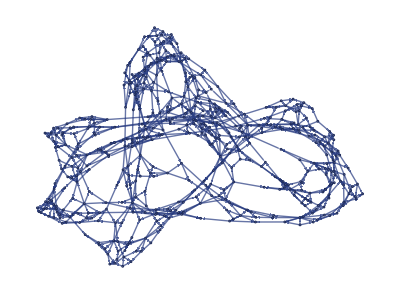

```mathematica
WolframModel[{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}},{{0,0},{0,0}},10,"FinalStatePlot"]
```

Visualize a Wolfram model rule:

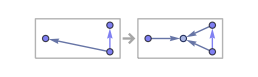

```mathematica
RulePlot[WolframModel[{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}}]]
```

Generate a symbolic representation of Wolfram model evolution:

```mathematica
evolution=WolframModel[{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}},{{0,0},{0,0}},10]
```

WolframModelEvolutionObject[…]

Find the state after 3 generations:

```mathematica
evolution[3]
```

{{0,3},{1,3},{0,2},{0,4},{1,4},{2,4},{0,1},{0,5},{2,5},{1,5},{1,3},{1,6},{2,6},{3,6}}

Find the casual graph for the evolution:

```mathematica
evolution["CausalGraph"]
```

-Graphics-

### Scope

#### Multiple rules

Multiple rules can be specified as a list of rules:

```mathematica
evolution=WolframModel[{{{1,1,2}}->{{2,2,1},{2,3,2},{1,2,3}},{{1,2,1},{3,4,2}}->{{4,3,2}}},{{1,1,1}},4]
```

WolframModelEvolutionObject[…]

To see which rules were used for each replacement:

```mathematica
evolution["AllEventsRuleIndices"]
```

{1,1,1,1,1,1,2,1,1,1,2,1,2}

#### Pattern rules

Use explicit patterns to specify rules:

```mathematica
WolframModel[<|"PatternRules"->{a_?EvenQ,b_?OddQ}:>{a+b,a-b}|>,{1,2,3,4,5},∞,"AllEventsStatesList"]
```

{{1,2,3,4,5},{3,4,5,3,1},{5,3,1,7,1}}

New vertices can be created with a Module:

```mathematica
WolframModel[<|"PatternRules"->{{a_,b_}}:>Module[{c},{{a,c},{c,b}}]|>,{{1,2}},3,"StatesList"]
```

{{{1,2}},{{1,v1019},{v1019,2}},{{1,v1020},{v1020,v1019},{v1019,v1021},{v1021,2}},{{1,v1022},{v1022,v1020},{v1020,v1023},{v1023,v1019},{v1019,v1024},{v1024,v1021},{v1021,v1025},{v1025,2}}}

#### Automatic initial state

An initial state consisting of an appropriate number of (hyper) self-loops can be automatically produced for anonymous (non-pattern) rules:

```mathematica
WolframModel[{{1,2},{1,2}}->{{3,2},{3,2},{2,1},{1,3}},Automatic,0][0]
```

{{1,1},{1,1}}

That even works for multiple rules in which case the loops are chosen in such a way that any of the rules can match:

```mathematica
WolframModel[{{{1,2},{1,2}}->{{3,2},{3,2},{2,1,3},{2,3}},{{2,1,3},{2,3}}->{{2,1},{1,3}}},Automatic,0][0]
```

{{1,1},{1,1},{1,1,1}}

#### Termination criteria

Run for 2 complete generations:

```mathematica
WolframModel[{{x,y}}->{{x,y},{y,z}},{{1,2}},2,"StatesList"]
```

{{{1,2}},{{1,2},{2,3}},{{1,2},{2,4},{2,3},{3,5}}}

Allow a total of 4 events:

```mathematica
WolframModel[{{x,y}}->{{x,y},{y,z}},{{1,2}},<|"MaxEvents"->4|>,"StatesList"]
```

{{{1,2}},{{1,2},{2,3}},{{1,2},{2,4},{2,3},{3,5}},{{2,4},{2,3},{3,5},{1,2},{2,6}}}

Stop either after 4 events, or when the state is about to exceed 5 vertices, whichever is sooner:

```mathematica
WolframModel[{{x,y}}->{{x,y},{y,z}},{{1,2}},<|"MaxEvents"->4,"MaxVertices"->5|>,"StatesList"]
```

{{{1,2}},{{1,2},{2,3}},{{1,2},{2,4},{2,3},{3,5}}}

Stop once the maximum vertex degree is about to exceed 20:

```mathematica
WolframModel[{{1,2},{1,2},{3,1}}->{{1,1},{1,4},{2,1},{2,4},{4,3}},{{1,1},{1,1},{1,1}},<|"MaxVertexDegree"->20|>]
```

WolframModelEvolutionObject[…]

#### Properties

"StatesList" yields the list of states at each generation:

```mathematica
WolframModel[{{x,y}}->{{x,y},{y,z}},{{1,2}},2,"StatesList"]
```

{{{1,2}},{{1,2},{2,3}},{{1,2},{2,4},{2,3},{3,5}}}

Make the list of plots of all states:

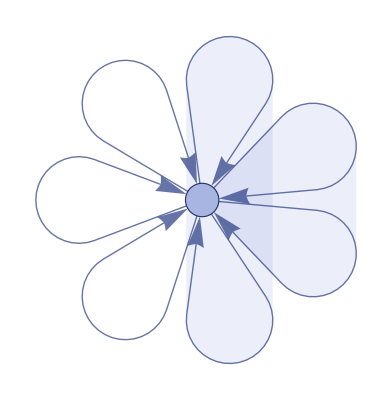
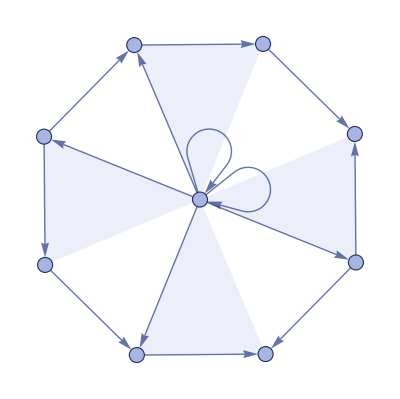
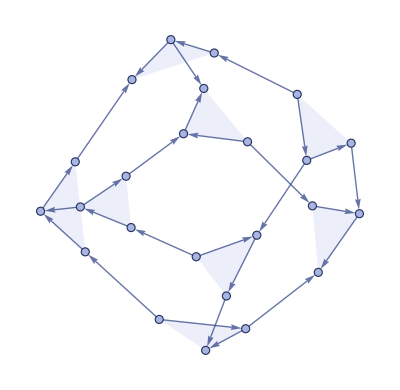
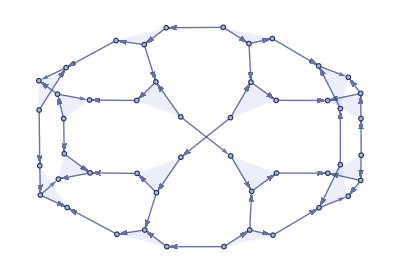
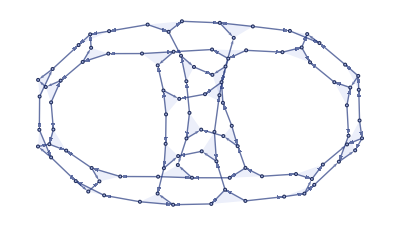
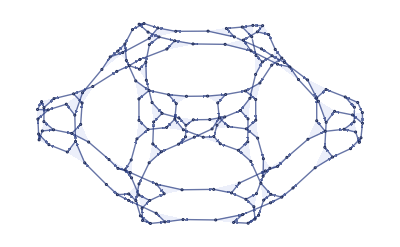

```mathematica
WolframModel[{{1,2,3},{4,5,6},{1,4}}->{{2,7,8},{3,9,10},{5,11,12},{6,13,14},{8,12},{11,10},{13,7},{14,9}},{{1,1,1},{1,1,1},{1,1},{1,1},{1,1}},5,"StatesPlotsList"]
```

"FinalState" yields the state obtained after all replacements of the evolution have been made:

```mathematica
WolframModel[{{1,2,3},{4,5,6},{1,4}}->{{2,7,8},{3,9,10},{5,11,12},{6,13,14},{8,12},{11,10},{13,7},{14,9}},{{1,1,1},{1,1,1},{1,1},{1,1},{1,1}},2,"FinalState"]
```

{{3,7},{6,5},{8,2},{9,4},{2,10,11},{3,12,13},{4,14,15},{5,16,17},{11,15},{14,13},{16,10},{17,12},{6,18,19},{7,20,21},{8,22,23},{9,24,25},{19,23},{22,21},{24,18},{25,20}}

Make the plot of the final state:

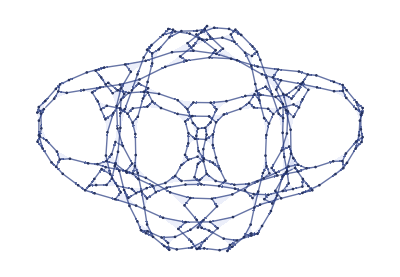

```mathematica
WolframModel[{{1,2,3},{4,5,6},{1,4}}->{{2,7,8},{3,9,10},{5,11,12},{6,13,14},{8,12},{11,10},{13,7},{14,9}},{{1,1,1},{1,1,1},{1,1},{1,1},{1,1}},6,"FinalStatePlot"]
```

"StatesList" shows a compressed version of the evolution. To see how state changes with each applied replacement, use "AllEventsStatesList":

```mathematica
WolframModel[{{x,y}}->{{x,y},{y,z}},{{1,2}},2,"AllEventsStatesList"]
```

{{{1,2}},{{1,2},{2,3}},{{2,3},{1,2},{2,4}},{{1,2},{2,4},{2,3},{3,5}}}

"AllEventsList" returns all replacement events throughout the evolution:

```mathematica
WolframModel[{{1,2}}->{{3,4},{3,1},{4,1},{2,4}},{{1,1}},2,"AllEventsList"]
```

{{1,{1}→{2,3,4,5}},{1,{2}→{6,7,8,9}},{1,{3}→{10,11,12,13}},{1,{4}→{14,15,16,17}},{1,{5}→{18,19,20,21}}}

"AllEventsRuleIndices" returns which rule was used for each event:

```mathematica
WolframModel[{{{1,1,2}}->{{2,2,1},{2,3,2},{1,2,3}},{{1,2,1},{3,4,2}}->{{4,3,2}}},{{1,1,1}},4,"AllEventsRuleIndices"]
```

{1,1,1,1,1,1,2,1,1,1,2,1,2}

"EventsStatesList" just produces a list of {event,state} pairs, where state is the complete state right after this event is applied:

```mathematica
WolframModel[{{1,2}}->{{3,4},{3,1},{4,1},{2,4}},{{1,1}},2,"EventsStatesList"]//Column
```

{{1,{1}→{2,3,4,5}},{2,3,4,5}}
{{1,{2}→{6,7,8,9}},{3,4,5,6,7,8,9}}
{{1,{3}→{10,11,12,13}},{4,5,6,7,8,9,10,11,12,13}}
{{1,{4}→{14,15,16,17}},{5,6,7,8,9,10,11,12,13,14,15,16,17}}
{{1,{5}→{18,19,20,21}},{6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}}

"EventsStatesPlotsList" plots not only the states, but also the events that produced them:

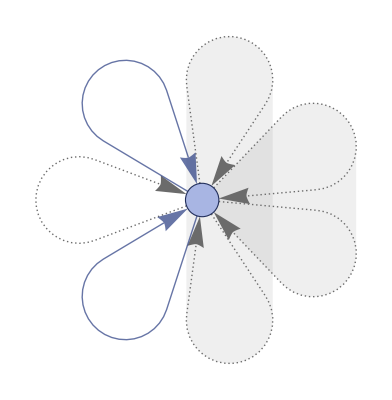
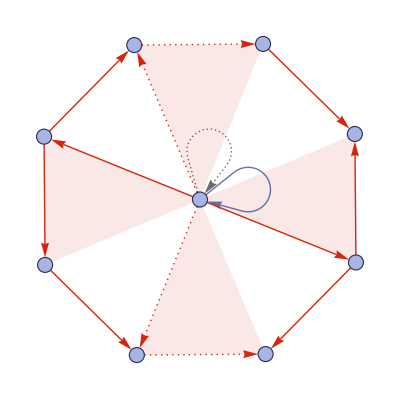
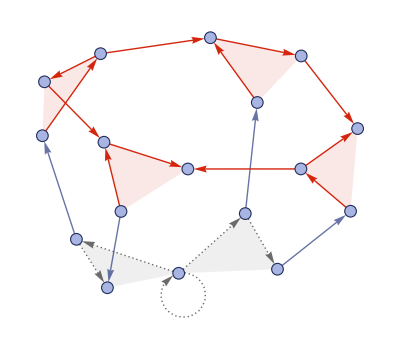
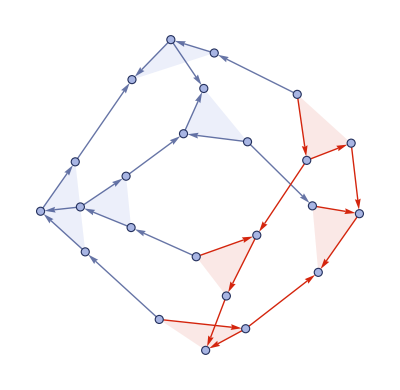

```mathematica
WolframModel[{{1,2,3},{4,5,6},{1,4}}->{{2,7,8},{3,9,10},{5,11,12},{6,13,14},{8,12},{11,10},{13,7},{14,9}},{{1,1,1},{1,1,1},{1,1},{1,1},{1,1}},2,"EventsStatesPlotsList"]
```

"AllEventsEdgesList" returns the list of edges throughout evolution:

```mathematica
WolframModel[{{x,y}}->{{x,y},{y,z}},{{1,2}},2,"AllEventsEdgesList"]
```

{{1,2},{1,2},{2,3},{1,2},{2,4},{2,3},{3,5}}

Get creator and destroyer events for each edge throughout the evolution:

```mathematica
WolframModel[{{x,y}}->{{x,y},{y,z}},{{1,2}},2,{"EdgeCreatorEventIndices","EdgeDestroyerEventIndices"}]
```

{{0,1,1,2,2,3,3},{1,2,3,∞,∞,∞,∞}}

"VertexCountList" and "EdgeCountList" return counts of vertices and edges respectively in each state of "StatesList":

```mathematica
WolframModel[{{1,2,3},{2,4,5}}->{{6,6,3},{2,6,2},{6,4,2},{5,3,6}},{{1,1,1},{1,1,1}},10,{"VertexCountList","EdgeCountList"}]
```

{{1,2,4,8,14,27,49,92,171,324,622},{2,4,8,16,28,54,98,184,342,648,1244}}

"GenerationsCount" returns both complete and partial generations count:

```mathematica
WolframModel[{{1,2}}->{{1,3},{1,3},{3,2}},{{1,1}},<|"MaxEvents"->42|>,"GenerationsCount"]
```

{4,1}

"GenerationEventsCountList" gives the number of events per each generation:

```mathematica
WolframModel[{{1,2}}->{{1,3},{1,3},{3,2}},{{1,1}},5,"GenerationEventsCountList"]
```

{1,3,9,27,81}

"GenerationEventsList" returns the same list of events, but splits them into sublists for each generation:

```mathematica
WolframModel[{{1,2}}->{{3,4},{3,1},{4,1},{2,4}},{{1,1}},2,"GenerationEventsList"]//Column
```

{{1,{1}→{2,3,4,5}}}
{{1,{2}→{6,7,8,9}},{1,{3}→{10,11,12,13}},{1,{4}→{14,15,16,17}},{1,{5}→{18,19,20,21}}}

"EdgeGenerationsList" yields the list of generation numbers for each edge in "AllEventsEdgesList":

```mathematica
WolframModel[{{1,2},{1,3},{1,4}}->{{2,2},{3,2},{3,4},{3,5}},{{1,1},{1,1},{1,1}},5,"EdgeGenerationsList"]
```

{0,0,0,1,1,1,1,2,2,2,2,3,3,3,3,4,4,4,4,5,5,5,5,5,5,5,5}

"EventsGenerationsList" gives the same for events:

```mathematica
WolframModel[{{1,2},{1,3},{1,4}}->{{2,2},{3,2},{3,4},{3,5}},{{1,1},{1,1},{1,1}},5,"EventGenerationsList"]
```

{1,2,3,4,5,5}

"AllEventsCount" returns the overall number of events throughout the evolution:

```mathematica
WolframModel[{{1,2}}->{{1,3},{1,3},{3,2}},{{1,1}},5,"AllEventsCount"]
```

121

Get a causal graph for an evolution:

```mathematica
WolframModel[{{1,2,3},{4,5,6},{1,4}}->{{3,7,8},{9,2,10},{11,12,5},{13,14,6},{7,12},{11,9},{13,10},{14,8}},{{1,1,1},{1,1,1},{1,1},{1,1},{1,1}},20,"CausalGraph"]
```

-Graphics-

The causal graph can be layered putting events from each generation on a different level:

```mathematica
WolframModel[{{1,2,3},{4,5,6},{1,4}}->{{3,7,8},{9,2,10},{11,12,5},{13,14,6},{7,12},{11,9},{13,10},{14,8}},{{1,1,1},{1,1,1},{1,1},{1,1},{1,1}},10,"LayeredCausalGraph"]
```

-Graphics-

### Options

#### VertexNamingFunction

Use symbolic names for new vertices:

```mathematica
WolframModel[{{1,2}}->{{1,3},{1,3},{3,2}},{{v1,v1}},2,"StatesList","VertexNamingFunction"->None]
```

{{{v1,v1}},{{v1,v6712},{v1,v6712},{v6712,v1}},{{v1,v6713},{v1,v6713},{v6713,v6712},{v1,v6714},{v1,v6714},{v6714,v6712},{v6712,v6715},{v6712,v6715},{v6715,v1}}}

Sequentially rename all vertices including the initial condition:

```mathematica
WolframModel[{{1,2}}->{{1,3},{1,3},{3,2}},{{v1,v1}},2,"StatesList","VertexNamingFunction"->All]
```

{{{1,1}},{{1,2},{1,2},{2,1}},{{1,3},{1,3},{3,2},{1,4},{1,4},{4,2},{2,5},{2,5},{5,1}}}

#### IncludePartialGenerations

Drop partial generations from the evolution:

```mathematica
WolframModel[{{1,2}}->{{1,3},{1,3},{3,2}},{{1,1}},<|"MaxEvents"->42|>,"IncludePartialGenerations"->False]
```

WolframModelEvolutionObject[…]

#### IncludeBoundaryEvents

Include the initial event in a causal graph:

```mathematica
WolframModel[<|"PatternRules"->{a_,b_}:>a+b|>,{3,8,8,8,2,10,0,9,7},Infinity,"LayeredCausalGraph","IncludeBoundaryEvents"->"Initial"]
```

-Graphics-

Include both the final event in the list of events:

```mathematica
WolframModel[<|"PatternRules"->{a_,b_}:>a+b|>,{3,8,8,8,2,10,0,9,7},Infinity,"AllEventsList","IncludeBoundaryEvents"->"Final"]
```

{{1,{1,2}→{10}},{1,{3,4}→{11}},{1,{5,6}→{12}},{1,{7,8}→{13}},{1,{9,10}→{14}},{1,{11,12}→{15}},{1,{13,14}→{16}},{1,{15,16}→{17}},{∞,{17}→{}}}

Include both the initial and the final events in "EventsStatesList":

```mathematica
WolframModel[{{1,2}}->{{3,4},{3,1},{4,1},{2,4}},{{1,1}},2,"EventsStatesList","IncludeBoundaryEvents"->All]//Column
```

{{0,{}→{1}},{1}}
{{1,{1}→{2,3,4,5}},{2,3,4,5}}
{{1,{2}→{6,7,8,9}},{3,4,5,6,7,8,9}}
{{1,{3}→{10,11,12,13}},{4,5,6,7,8,9,10,11,12,13}}
{{1,{4}→{14,15,16,17}},{5,6,7,8,9,10,11,12,13,14,15,16,17}}
{{1,{5}→{18,19,20,21}},{6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}}
{{∞,{6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}→{}},{}}

#### Method

Use symbolic implementation to compute the evolution (which is faster if vertex degrees are large):

```mathematica
WolframModel[{{{0}}->{{0},{0},{0}},{{0},{0},{0}}->{{0}}},{{0}},<|"MaxEvents"->30|>,Method->"Symbolic"]//AbsoluteTiming
```

{0.011673,WolframModelEvolutionObject[…]}

Compare:

```mathematica
WolframModel[{{{0}}->{{0},{0},{0}},{{0},{0},{0}}->{{0}}},{{0}},<|"MaxEvents"->30|>]//AbsoluteTiming
```

{7.2508,WolframModelEvolutionObject[…]}

#### TimeConstraint

Return the evolution object after running the evolution for 1 second:

```mathematica
WolframModel[{{1,2}}->{{1,3},{1,3},{3,2}},{{1,1}},Infinity,TimeConstraint->1]
```

WolframModelEvolutionObject[<|CreatorEvents -> {0, 1, 1, 1, 2, 2, 2, 3, 3, 3, 4, 4, 4, 5, 5, 5, 6, 6, 6, 7, 7, 7, 8, 8, 8, 9, 9, 9, 10, 10, 10, 11, 11, 11, 12, 12, 12, 13, 13, 13, 14, 14, 14, 15, 15, <<37334>>, 12460, 12460, 12461, 12461, 12461, 12462, 12462, 12462, 12463, 12463, 12463, 12464, 12464, 12464, 12465, 12465, 12465, 12466, 12466, 12466, 12467, 12467, 12467}, <<7>>|>]

#### EventOrderingFunction

Show final states from 5 random event orderings:

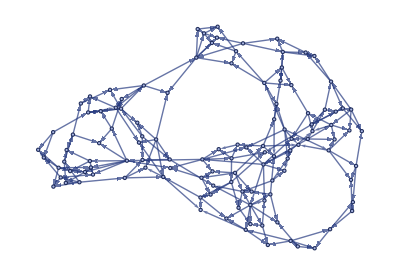
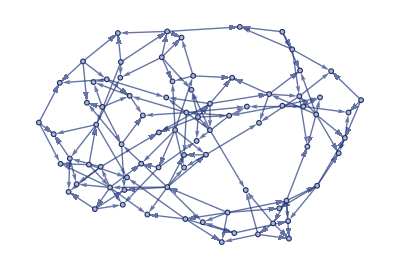
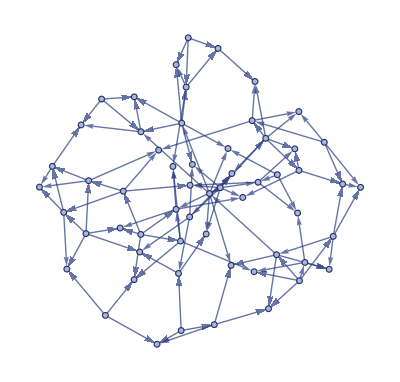
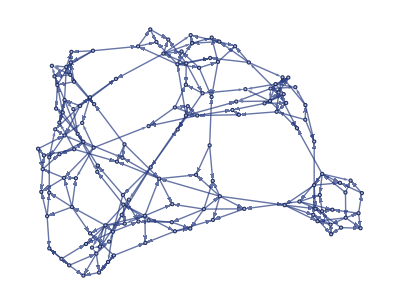
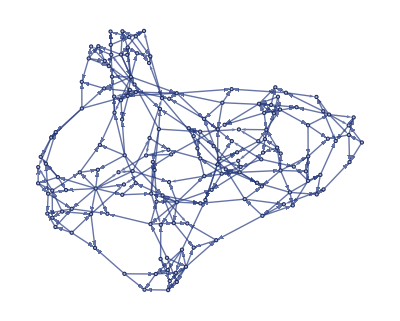

```mathematica
Table[WolframModel[{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}},{{0,0},{0,0}},10,"FinalStatePlot","EventOrderingFunction"->"Random"],5]
```

Compare results for the default ordering with the "RuleOrdering":

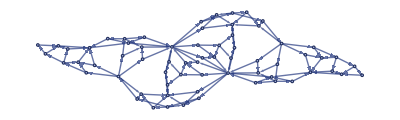
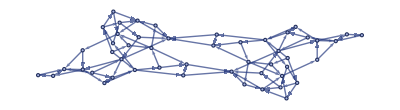

```mathematica
WolframModel[{{1,2},{2,3}}->{{4,2},{4,1},{2,1},{3,4}},{{1,2},{2,3},{3,4},{4,1}},5,"FinalStatePlot","EventOrderingFunction"->#]&/@{Automatic,"RuleOrdering"}
```

### Properties and Relations

Use ResourceFunction["WolframModelPlot"] to visualize states of WolframModel:

```mathematica
{{"[◼]", "WolframModelPlot"}}/@WolframModel[{{1,2},{2,3}}->{{4,2},{4,1},{2,1},{3,4}},{{1,2},{2,3},{3,4},{4,1}},7,"StatesList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Get an evolution object:

```mathematica
evolution=WolframModel[{{1,2},{2,3}}->{{4,2},{4,1},{2,1},{3,4}},{{1,2},{2,3},{3,4},{4,1}},7]
```

WolframModelEvolutionObject[…]

Extract the state after 100 events from the object:

```mathematica
{{"[◼]", "WolframModelPlot"}}[evolution["StateAfterEvent",100]]
```

-Graphics-

Use RulePlot to visualize the rule:

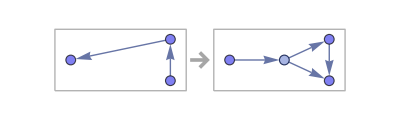

```mathematica
RulePlot[WolframModel[{{1,2},{2,3}}->{{4,2},{4,1},{2,1},{3,4}}]]
```

### Possible Issues

The evolution order (and hence the result) might change after canonicalization of the rule:

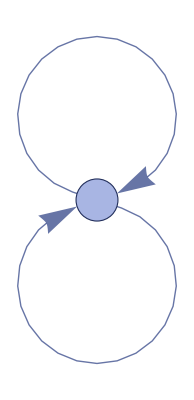
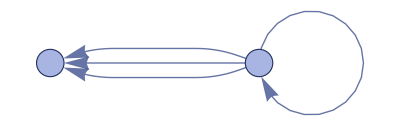
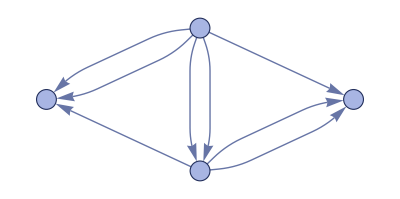
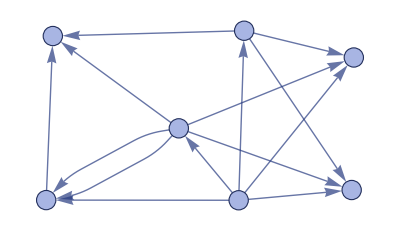

```mathematica
WolframModel[{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}},Automatic,3,"StatesPlotsList"]
```

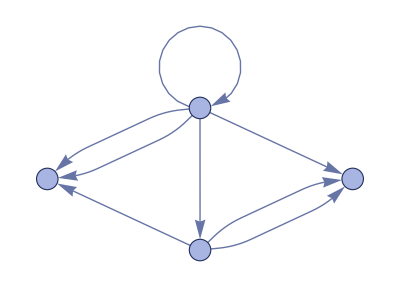
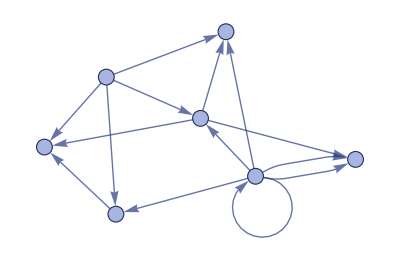
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
WolframModel[{{"[◼]", "FindCanonicalWolframModel"}}[{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}}],Automatic,3,"StatesPlotsList"]
```

Using custom step limiters might produce a state in-between generations:

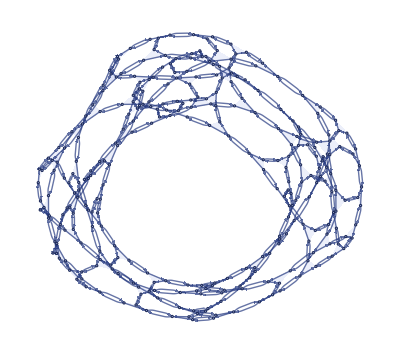

```mathematica
WolframModel[{{1,2,3},{4,5,6},{2,5},{5,2}}->{{7,1,8},{9,3,10},{11,4,12},{13,6,14},{7,13},{13,7},{8,10},{10,8},{9,11},{11,9},{12,14},{14,12}},{{1,2,3},{4,5,6},{1,4},{4,1},{2,5},{5,2},{3,6},{6,3}},<|"MaxVertices"->300,"MaxEvents"->200|>,"FinalStatePlot"]
```

Set "IncludePartialGenerations"→False to drop partial generations:

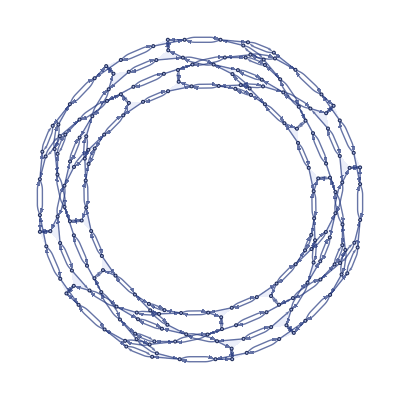

```mathematica
WolframModel[{{1,2,3},{4,5,6},{2,5},{5,2}}->{{7,1,8},{9,3,10},{11,4,12},{13,6,14},{7,13},{13,7},{8,10},{10,8},{9,11},{11,9},{12,14},{14,12}},{{1,2,3},{4,5,6},{1,4},{4,1},{2,5},{5,2},{3,6},{6,3}},<|"MaxVertices"->300,"MaxEvents"->200|>,"FinalStatePlot","IncludePartialGenerations"->False]
```

Options for properties like "CausalGraph" cannot be given in WolframModel:

```mathematica
WolframModel[{{1,2,3},{4,5,6},{1,4}}->{{3,7,8},{9,2,10},{11,12,5},{13,14,6},{7,12},{11,9},{13,10},{14,8}},{{1,1,1},{1,1,1},{1,1},{1,1},{1,1}},12,"CausalGraph",VertexLabels->Automatic]
```

WolframModel::optx: Unknown option VertexLabels→Automatic in WolframModel[{{1,2,3},{4,5,6},{1,4}}→{{3,7,8},{9,2,10},{11,12,5},{13,14,6},{7,12},{11,9},{13,10},{14,8}},{{1,1,1},{1,1,1},{1,1},{1,1},{1,1}},12,CausalGraph,VertexLabels→Automatic].

WolframModel[{{1,2,3},{4,5,6},{1,4}}→{{3,7,8},{9,2,10},{11,12,5},{13,14,6},{7,12},{11,9},{13,10},{14,8}},{{1,1,1},{1,1,1},{1,1},{1,1},{1,1}},12,CausalGraph,VertexLabels→Automatic]

The options can be given to an evolution object however:

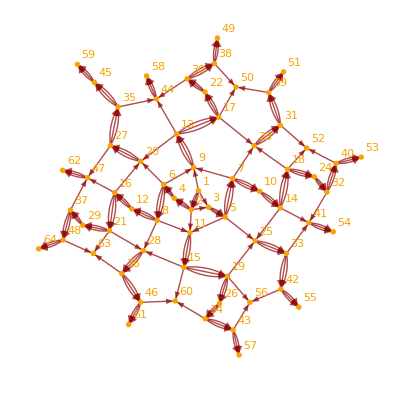

```mathematica
WolframModel[{{1,2,3},{4,5,6},{1,4}}->{{3,7,8},{9,2,10},{11,12,5},{13,14,6},{7,12},{11,9},{13,10},{14,8}},{{1,1,1},{1,1,1},{1,1},{1,1},{1,1}},12]["CausalGraph",VertexLabels->Automatic]
```

"FinalDistinctElementsCount" is not equivalent to "FinalVertexCount":

```mathematica
WolframModel[<|"PatternRules"->{{a_}}:>{{a+1},{a-1},{{a+2,a-2}}}|>,{{1}},7,"VertexCountList"]
```

{1,3,6,10,15,21,28,36}

```mathematica
WolframModel[<|"PatternRules"->{{a_}}:>{{a+1},{a-1},{{a+2,a-2}}}|>,{{1}},#,"FinalDistinctElementsCount"]&/@Range[0,7]
```

{1,4,9,13,17,21,25,29}

That happens if non-trivial nesting is present, and the following is counted as 3 vertices but 4 distinct elements:

```mathematica
WolframModel[<|"PatternRules"->{{a_}}:>{{a+1},{a-1},{{a+2,a-2}}}|>,{{1}},1,"FinalState"]
```

{{2},{0},{{3,-1}}}

The "LowLevel" implementation (the default) is slow if the number of potential matches is very large (which could occur in states with large vertex degrees):

```mathematica
AbsoluteTiming[WolframModel[{{{0}}->{{0},{0},{0}},{{0},{0},{0}}->{{0}}},{{0}},<|"MaxEvents"->30|>,Method->"LowLevel"]]
```

{7.07931,WolframModelEvolutionObject[…]}

The "Symbolic" implementation might help in such cases:

```mathematica
AbsoluteTiming[WolframModel[{{{0}}->{{0},{0},{0}},{{0},{0},{0}}->{{0}}},{{0}},<|"MaxEvents"->30|>,Method->"Symbolic"]]
```

{0.011562,WolframModelEvolutionObject[…]}

A single "EventOrderingFunction" might be insufficient to select a single event and produce deterministic evolution:

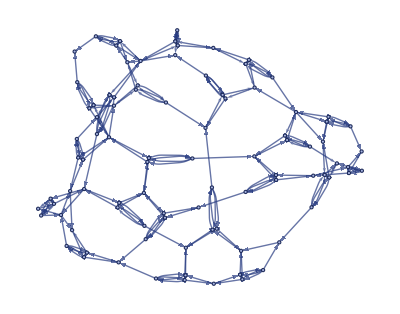
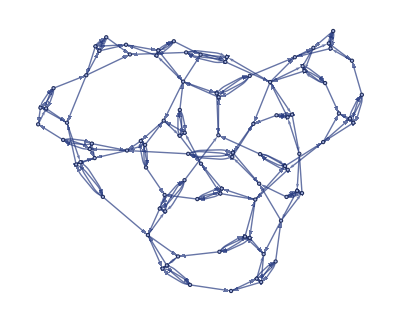
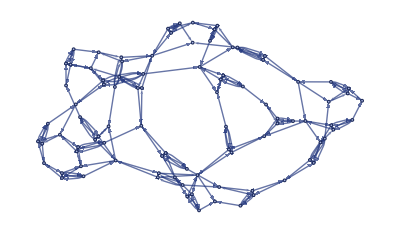

```mathematica
Table[WolframModel[{{{1,2},{1,3},{1,4}}->{{5,6},{6,7},{7,5},{5,7},{7,6},{6,5},{5,2},{6,3},{7,4},{2,7},{4,5}},{{1,2},{1,3},{1,4},{1,5}}->{{2,3},{3,4}}},{{1,1},{1,1},{1,1}},<|"MaxEvents"->30|>,"FinalStatePlot","EventOrderingFunction"->"LeastRecentEdge"],3]
```

Use multiple ordering functions to get deterministic behavior:

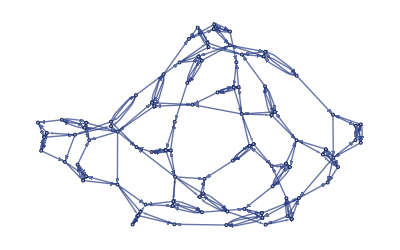
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[WolframModel[{{{1,2},{1,3},{1,4}}->{{5,6},{6,7},{7,5},{5,7},{7,6},{6,5},{5,2},{6,3},{7,4},{2,7},{4,5}},{{1,2},{1,3},{1,4},{1,5}}->{{2,3},{3,4}}},{{1,1},{1,1},{1,1}},<|"MaxEvents"->30|>,"FinalStatePlot","EventOrderingFunction"->{"LeastRecentEdge","RuleOrdering"}],3]
```

### Neat Examples

Make a causal graph for a system that computes Total of a list of numbers:

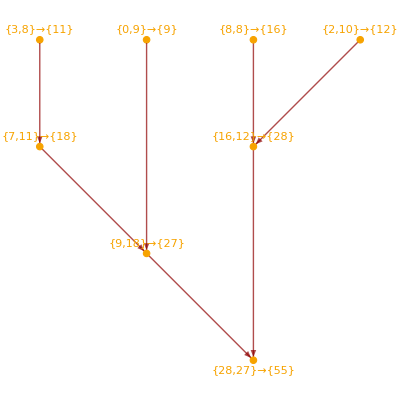

```mathematica
With[{evolution=WolframModel[<|"PatternRules"->{a_,b_}:>a+b|>,{3,8,8,8,2,10,0,9,7},Infinity]},With[{causalGraph=evolution["LayeredCausalGraph"]},Graph[causalGraph,VertexLabels->Thread[VertexList[causalGraph]->Map[evolution["AllEventsEdgesList"][[#]]&,Last/@evolution["AllEventsList"],{2}]]]]]
```

Show which rule is used for each event on a causal graph:

```mathematica
With[{evolution=WolframModel[{{{1,1,2}}->{{2,2,1},{2,3,2},{1,2,3}},{{1,2,1},{3,4,2}}->{{4,3,2}}},{{1,1,1}},6]},With[{causalGraph=evolution["LayeredCausalGraph"]},Graph[causalGraph,VertexStyle->Thread[VertexList[causalGraph]->Replace[evolution["AllEventsRuleIndices"],{1->Black,2->White},{1}]],VertexSize->Medium]]]
```

-Graphics-

Color edges of different generations differently in a "StatesPlotsList":

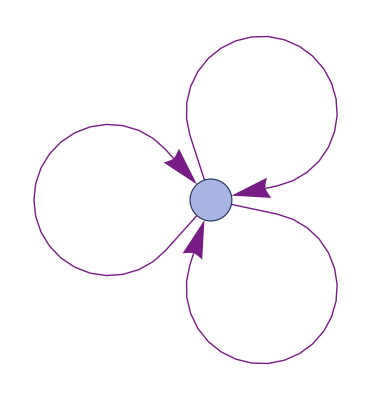
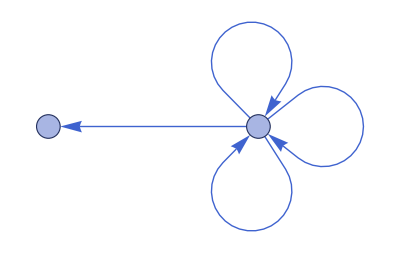
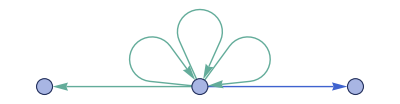
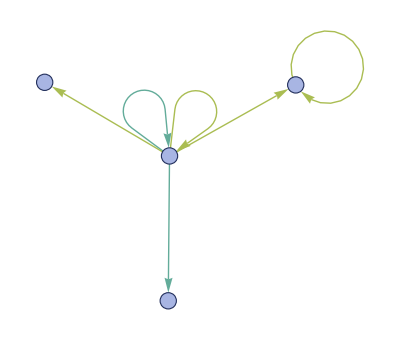
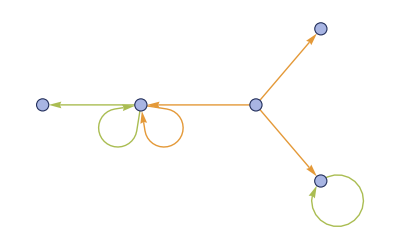
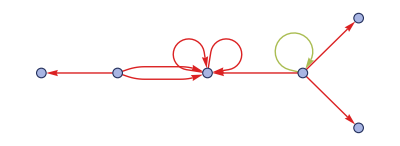

```mathematica
With[{evolution=WolframModel[{{1,2},{1,3},{1,4}}->{{2,2},{3,2},{3,4},{3,5}},{{1,1},{1,1},{1,1}},5]},MapThread[{{"[◼]", "WolframModelPlot"}}[#,EdgeStyle->#2]&,{evolution["StatesList"],Replace[evolution["EdgeGenerationsList"][[#]]&/@(evolution["StateEdgeIndicesAfterEvent",#]&)/@Prepend[0]@Accumulate@evolution["GenerationEventsCountList"],g_:>ColorData["Rainbow"][g/5],{2}]}]]
```

Plot a result of a uniformly random evolution trimmed at a complete number of generations:

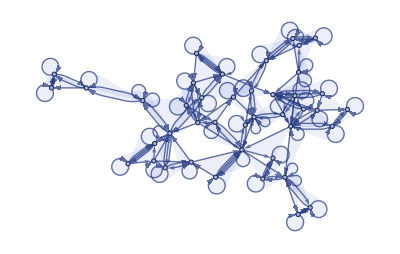

```mathematica
WolframModel[{{1,2,3},{2,4,5}}->{{6,6,3},{2,6,2},{6,4,2},{5,3,6}},{{1,1,1},{1,1,1}},<|"MaxEvents"->10000|>,"FinalStatePlot","EventOrderingFunction"->"Random","IncludePartialGenerations"->False]
```

Show the result of an evolution for all single event ordering functions:

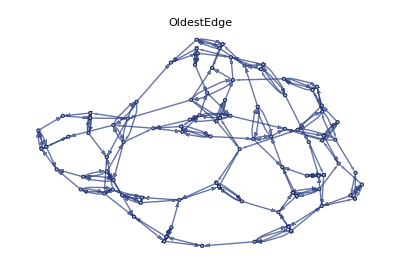
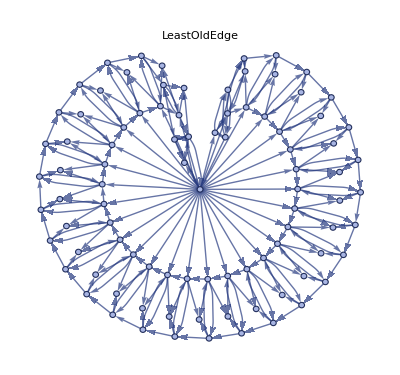
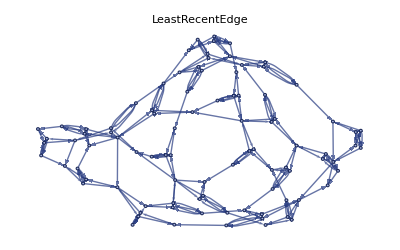
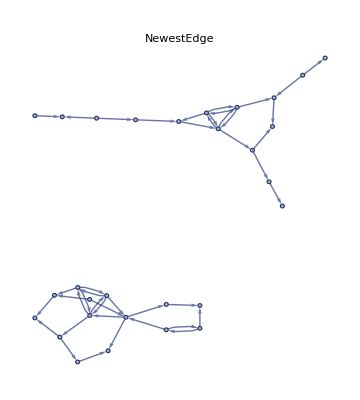
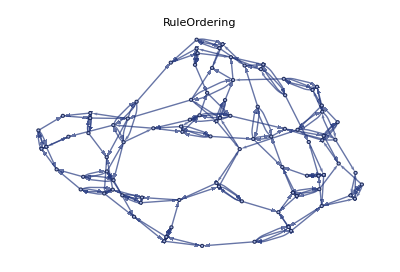
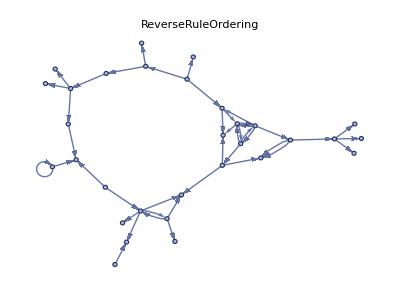
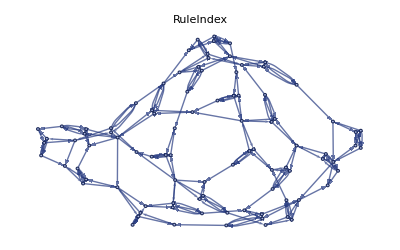
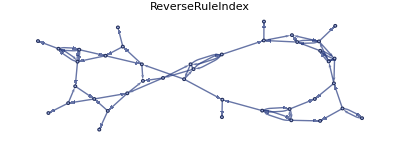

```mathematica
WolframModel[{{{1,2},{1,3},{1,4}}->{{5,6},{6,7},{7,5},{5,7},{7,6},{6,5},{5,2},{6,3},{7,4},{2,7},{4,5}},{{1,2},{1,3},{1,4},{1,5}}->{{2,3},{3,4}}},{{1,1},{1,1},{1,1}},<|"MaxEvents"->30|>,"EventOrderingFunction"->{#,"LeastRecentEdge","RuleOrdering","RuleIndex"}]["FinalStatePlot",PlotLabel->#]&/@{"OldestEdge","LeastOldEdge","LeastRecentEdge","NewestEdge","RuleOrdering","ReverseRuleOrdering","RuleIndex","ReverseRuleIndex","Random"}
```

## Source & Additional Information

### Contributed ByContributed ByEnter the name of the person, people or organization that should be publicly credited with contributing this function.

Stephen Wolfram & Max Piskunov

### KeywordsKeywordsList relevant terms (e.g. functional areas, algorithm names, related concepts) that should be used to include the function in search results.

fundamental physics

### Categories

Graphs & Networks

Higher Mathematical Computation

### Related SymbolsRelated SymbolsList up to twenty documented, system-level Wolfram Language symbols related to the function.

SubstitutionSystem

### Related Resource ObjectsRelated Resource ObjectsList the names of published resource objects from any Wolfram repository that are related to this function.

WolframModelPlot

RandomWolframModel

WolframModelEvolutionObject

### Source/Reference CitationSource/Reference CitationGive a bibliographic-style citation for the original source of the function and/or its components (e.g. a published paper, algorithm, or code repository).

Source, reference or citation information

### LinksLinksList additional URLs or hyperlinks for external information related to the function.

Link to other related material

### TestsTestsSpecify an optional list of tests for verifying that the function is working properly in any environment. Tests can be specified as Input/Output cell pairs or as symbolic VerificationTest expressions for including additional options.

```mathematica
MyFunction[x,y]
```

x y

## Author Notes

Additional information about limitations, issues, etc.

## Submission NotesSubmission NotesEnter any additional information that you would like to communicate to the reviewer here. This section will not be included in the published resource.

Additional information for the reviewer.